```mathematica
simplifiedldf = lw+pw^3 1/n(1+b Subscript[b, c] )+pw (-1+b/Subscript[b, c])
simplifiedldf1 =l+b p+a p^3
S = Solve[simplifiedldf1==0,p];
```

lw+pw (-1+b/b_c)+(pw^3 (1+b b_c))/n

l+b p+a p^3

```mathematica
l+b p+a p^3
```

l+b p+a p^3

```mathematica
sr1 = S[[1]][[1]];
sr2 = S[[2]][[1]];
sr3 = S[[3]][[1]];
ss1 = p/.sr1/.c->1;
ss2 = p/.sr2;
ss3 =p/.sr3/.c->1;
```

```mathematica
ss3
```

((1-ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 a^2 l+√3 √(4 a^3 b^3+27 a^4 l^2))^(1/3))-((1+ⅈ √3) (-9 a^2 l+√3 √(4 a^3 b^3+27 a^4 l^2))^(1/3))/(2 2^(1/3) 3^(2/3) a)

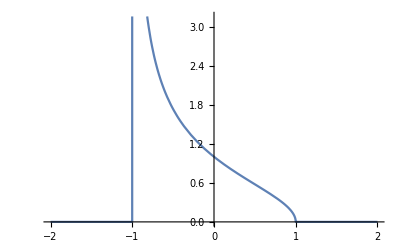

```mathematica
Plot[{-(2^(1/3) (-3+3 b^2))/(3 (1+b) (-27 l-54 b l-27 b^2 l+√(4 (-3+3 b^2)^3+(-27 l-54 b l-27 b^2 l)^2))^(1/3))+((-27 l-54 b l-27 b^2 l+√(4 (-3+3 b^2)^3+(-27 l-54 b l-27 b^2 l)^2))^(1/3))/(3 2^(1/3) (1+b))}/.l-> 0,{b,-2,2}]
```

```mathematica
vf1 = {u,p^3 +p(1-b) }
vf1/.b-> 0
```

{u,(1+b) p+p^3}

{u,p+p^3}

```mathematica
ss1
```

-(2^(1/3) (-3+3 b^2))/(3 (1+b) (-27 l-54 b l-27 b^2 l+√(4 (-3+3 b^2)^3+(-27 l-54 b l-27 b^2 l)^2))^(1/3))+((-27 l-54 b l-27 b^2 l+√(4 (-3+3 b^2)^3+(-27 l-54 b l-27 b^2 l)^2))^(1/3))/(3 2^(1/3) (1+b))

```mathematica
0
```

```mathematica
Manipulate[Module[{x0,y0}, x0 =-(2^(1/3) (-3+3 b^2))/(3 (1+b) (-27 l-54 b l-27 b^2 l+√(4 (-3+3 b^2)^3+(-27 l-54 b l-27 b^2 l)^2))^(1/3))+((-27 l-54 b l-27 b^2 l+√(4 (-3+3 b^2)^3+(-27 l-54 b l-27 b^2 l)^2))^(1/3))/(3 2^(1/3) (1+b)); y0 = 0;
Grid[{{Row[{"xCoord = ",Re[x0]," yCoord =",y0}]},{StreamPlot[ {-(l+p^3 +p (b-1 )),-(3 p^2 u+u (b-1 ))},{p,-1.5,1.5},{u,-0.5,0.5},StreamPoints->128,Epilog->{Green,PointSize[.04],Point[{x0,y0}]},ImageSize->500,PerformanceGoal->"Quality",StreamColorFunction->"Rainbow"]}}]
]
,{b,0,2},{l,-2,2}
]
```

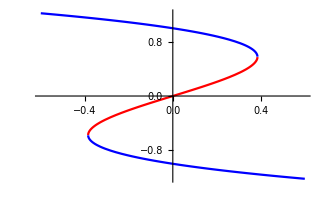

```mathematica
Plot[{ss1/.b-> 0,ss2/.b-> 0 ,ss3/.b-> 0},{l,-0.6,0.6},PlotStyle->{Blue,Blue,Red}]
```

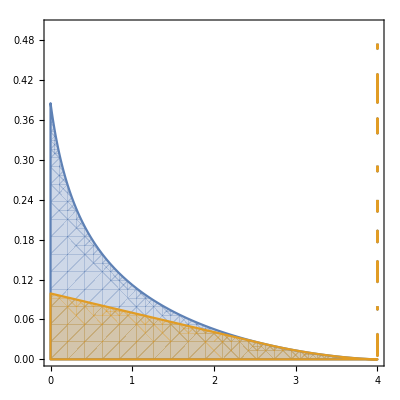

```mathematica
RegionPlot[{Re[ss1]>Re[ss3],(Re[ss3]<0.1 && Re[ss1]>Re[ss3])},{b,0,4},{l,0,0.5}]
```

```mathematica
NSolve[x^3-x==0,x]
```

{{x→-1.},{x→0.},{x→1.}}

```mathematica
Manipulate[Show[{Plot[{-((2/3)^(1/3) b)/((-9 a^2 l+√3 √(4 a^3 b^3+27 a^4 l^2))^(1/3))+((-9 a^2 l+√3 √(4 a^3 b^3+27 a^4 l^2))^(1/3))/(2^(1/3) 3^(2/3) a),
((1-ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 a^2 l+√3 √(4 a^3 b^3+27 a^4 l^2))^(1/3))-((1+ⅈ √3) (-9 a^2 l+√3 √(4 a^3 b^3+27 a^4 l^2))^(1/3))/(2 2^(1/3) 3^(2/3) a)},{b,-1,1},Frame-> True,PlotStyle->{{Black,Thick}},PlotRange-> {0,1.5},BaseStyle->{FontSize->20,FontFamily->"Times"},LabelStyle->{FontSize->20,FontFamily->"Times",Black},FrameLabel->{"β-α","\*SubscriptBox[\(p\), \(W\)]"},PlotLabel->"Phase Portrait"],
StreamPlot[ {0,-(a p^3 + b p+l)},{b,-1,1},{p,0,1.5},StreamPoints->{{{{0.5,1},Red},{{-0.5,1},Green},{{-0.75,1},Blue},Automatic}}, StreamScale->Large,ImageSize->1500,PerformanceGoal->"Speed"]},PlotRange-> Automatic]
,{l,0,2},{a,0.001,1}
]
```